# Fortran Flow Reader

```mathematica
(*put "no file" if the flux file doesn't exist*)
(*...................................................IRENE......................................................*)


(*...................................................FLOYD.......................................................*)
spinupinputfile="D:\\Dropbox\\Floyd\\river_fluxes\\spinup.txt";
hurricaneinputfile="D:\\Dropbox\\Floyd\\river_fluxes\\hurricane.txt";
spindowninputfile="D:\\Dropbox\\Floyd\\river_fluxes\\spindown.txt";
outputfile="D:\\Dropbox\\Floyd\\river_fluxes\\combined.txt";
filestarttime="Sep 13, 1999"//AbsoluteTime;
rundays=31+6+30;


(*...................................................10CMS TEST CASE......................................................*)
(*spinupinputfile="C:\\Users\\Sam\\Desktop\\Thesis Work\\ADCIRC\\10cms test\\10cms.flux";
hurricaneinputfile="C:\\Users\\Sam\\Desktop\\Thesis Work\\ADCIRC\\10cms test\\10cms.flux";
spindowninputfile="C:\\Users\\Sam\\Desktop\\Thesis Work\\ADCIRC\\10cms test\\10cms.flux";
outputfile="C:\\Users\\Sam\\Desktop\\Thesis Work\\ADCIRC\\10cms test\\mathematica_Q_scatters";
filestarttime="July 06, 2011"//AbsoluteTime;
rundays=10;*)


segmentlengths={12,8,11,12,14,13,14,6,6,30,30,64,63};(*number of nodes in each segment*)
nsegs=Length[segmentlengths];
Js=segmentlengths-1; (*number of element faces in each segment*)
nodestringnames={"Tar At Greenville","Tar At Pamlico","Tar At Tarboro","Tar Handoff +5 Nodes","Tar Handoff +10 Nodes","Fishing Handoff +5 Nodes","Fishing Handoff +10 Nodes","Tar Handoff","Fishing Handoff","Qout Tar Left Bank","Qout Tar Right Bank","Tar Internal Zig","confluence circle" };
signs={-1,1,-1,1,1,-1,1,1,1,-1,1,1,1};
fileendtime=filestarttime+rundays*24*60*60;
```

```mathematica
(*step 1- import spinup file*)
inp={spinupinputfile,hurricaneinputfile,spindowninputfile};

Qgrab=Table[0,{Length[inp]}];
Do[
inputfile=inp[[storm]];





Qgrab[[storm]]=Catch[


If[inputfile=="no file",
Throw["error - no file selected"];
];

in=OpenRead[inputfile];
(*STEP 1 - CHECK FOR COMPLETENESS*)
junk=Read[in,String];
stepsheader=Read[in,Number];
junk=Read[in,String];



(*get filelength*)
entries=ReadList[in,String];(*these are all the individual entries*)
filelength=Length[entries];
(*figure out how many output entries there are in the file*)
(*the file has 2 header lines*)

(*at each timestep, there is one line plus one for each segment node*)
perstep=1+Sum[segmentlengths[[i]],{i,1,Length[segmentlengths]}];
nsteps=filelength/perstep;
If[nsteps≠stepsheader,
Print[StringJoin["error-steps don't match",ToString[storm]]];
];

(*now that we know the number of lines in each step (perstep) we can import all the data*) 
Close[in];






in=OpenRead[inputfile];

outputlist={"header",Table[0,{nsegs}]};

header=Read[in,String];
junk=Read[in,String];
raw=ReadList[in,Word];
Close[in]
(*clean the entries*)
Do[
If[raw[[i]]=="NaN",
raw[[i]]=-9999,
raw[[i]]=StringReplace[raw[[i]],{"E+"->"*^","E-"->"*^-"}];
raw[[i]]=raw[[i]]//ToExpression]
,{i,1,Length[raw]}];



(*step 1 - partition raw into each timestep entry.*)
(*the quick way to do this is to use nsteps and filelength to get the entries per step.*)
(*note that we can't just use the prior value of "perstep" because at this point, *)
(* "perstep" is in lines, and we need it in numbers*)
(*e.g. each timestep line is one line, 2 numbers, etc*)
perstep=Length[raw]/nsteps;
raw=Partition[raw,perstep];
raw=Transpose[raw];
(*now raw is a bunch of vectorized entries with the following form*)
(*
time
timestep
(for i = 1 -> nsegs)
node i,1
node i,2
node i,3
....
node i,J(i)
segmentnumber(i)
avg_depth(i)
avg_V(i)
segment_Q(i)
*)


(*from that vectorization, it becomes clear that the index of each segment_Q(i) is as follows:
2 (time+timestep)
plus the number of nodes of each preceeding segment, including the one itself
+Sum(J(i'), i' 1->i)
plus three for each preceeding segment, including the one itself
+3*i
plus one for each preceeding segment_Q
+(i-1)
*)
Qindices=Table[2
+Sum[Js[[i2]],{i2,1,i}]
+3*i
+(i)
,{i,1,nsegs}];


times=raw[[1]];
times=times+filestarttime;
endtime=times[[Length[times]]];

Qseries=Table[{times,signs[[i]]*raw[[Qindices[[i]]]]}//Transpose,{i,1,Length[Qindices]}];
Throw[Qseries];



]

,{storm,1,Length[inp]}];
```

error-steps don't match3

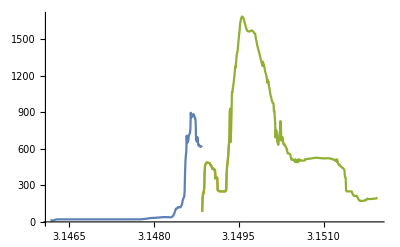

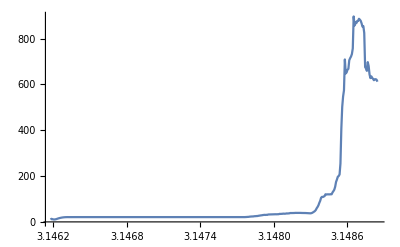

```mathematica
ListPlot[Qgrab[[1;;3,3]],Joined->True,PlotRange->All]
ListPlot[Qgrab[[1,3]],Joined->True,PlotRange->All]
```

```mathematica
Qgrab[[1,2,3]]
```

{3.51892×10^9,15.0021}

```mathematica
s=OpenWrite["C:\\Users\\Sam\\Desktop\\Thesis Work\\irene\\tarboro flux.txt"];
Do[
Do[
Write[s,DateString[Qgrab[[i,3,j,1]]],Qgrab[[i,3,j,2]]];
,{j,1,Length[Qgrab[[i,3]]]}];
,{i,1,3}];
Close[s];
```

```mathematica
Qgrab[[Length[Qgrab]]]
```

error-steps don't match

# Tar At Greenville

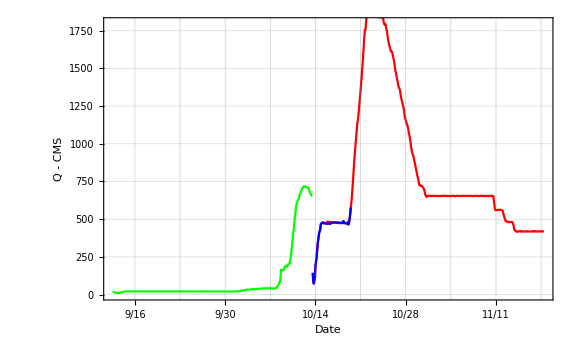

```mathematica
i=1;
Show[
scatterplot[Qgrab[[3,i]],filestarttime,fileendtime,0,1800,"Q - CMS","Date",nodestringnames[[i]],7,True,Red],
scatterplot[Qgrab[[2,i]],filestarttime,fileendtime,0,1800,"Q - CMS","Date",nodestringnames[[i]],7,True,Blue],
scatterplot[Qgrab[[1,i]],filestarttime,fileendtime,0,1800,"Q - CMS","Date",nodestringnames[[i]],7,True,Green]
]
```

# Tar At Pamlico

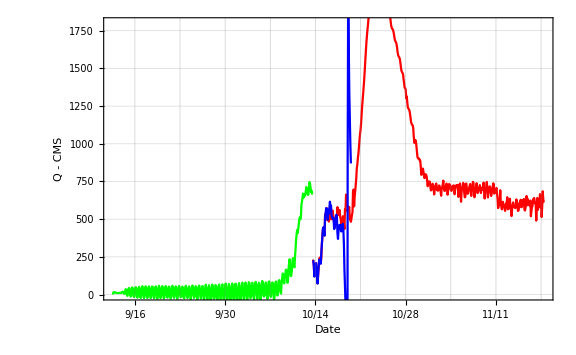

```mathematica
i=2;
Show[
scatterplot[Qgrab[[3,i]],filestarttime,fileendtime,0,1800,"Q - CMS","Date",nodestringnames[[i]],7,True,Red],
scatterplot[Qgrab[[2,i]],filestarttime,fileendtime,0,1800,"Q - CMS","Date",nodestringnames[[i]],7,True,Blue],
scatterplot[Qgrab[[1,i]],filestarttime,fileendtime,0,1800,"Q - CMS","Date",nodestringnames[[i]],7,True,Green]
]
```

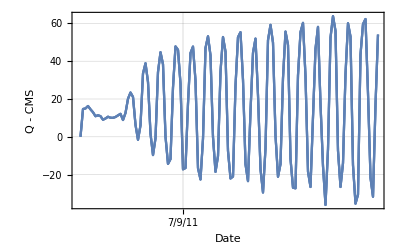

# Tar At Tarboro

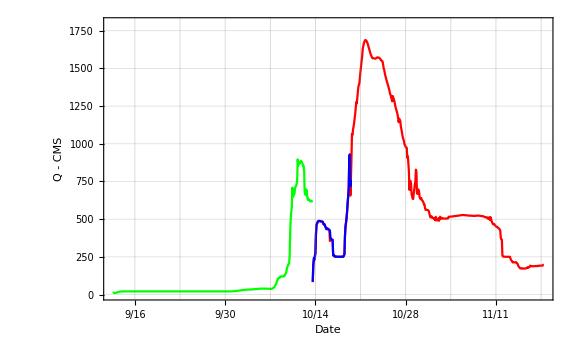

```mathematica
i=3;
Show[
scatterplot[Qgrab[[3,i]],filestarttime,fileendtime,0,1800,"Q - CMS","Date",nodestringnames[[i]],7,True,Red],
scatterplot[Qgrab[[2,i]],filestarttime,fileendtime,0,1800,"Q - CMS","Date",nodestringnames[[i]],7,True,Blue],
scatterplot[Qgrab[[1,i]],filestarttime,fileendtime,0,1800,"Q - CMS","Date",nodestringnames[[i]],7,True,Green]
]
```

# Tar Handoff

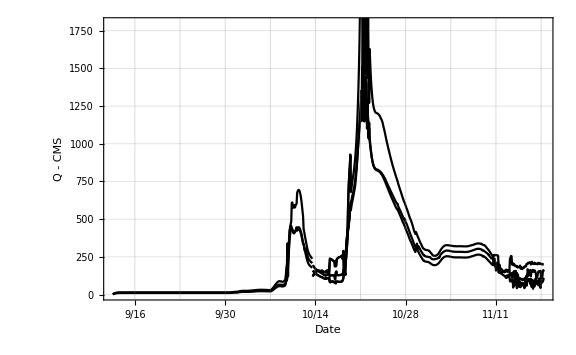
{{Null^2 -Graphics-},{□}}

```mathematica
{{i=8;
klist={8,4,5};

Show[
Table[
Table[
scatterplot[Qgrab[[j,klist[[k]]]],filestarttime,fileendtime,0,1800,"Q - CMS","Date",nodestringnames[[klist[[k]]]],7,True,Black],
{j,3,1,-1}]
,{k,1,3}]

]}, {□}}
```

# Fishing Handoff

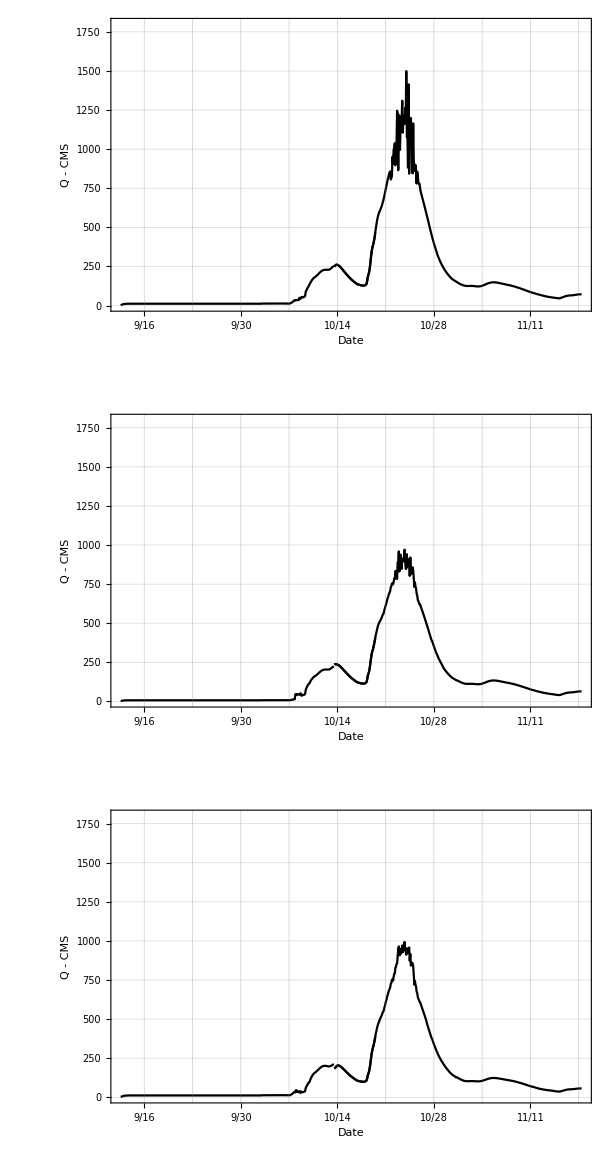

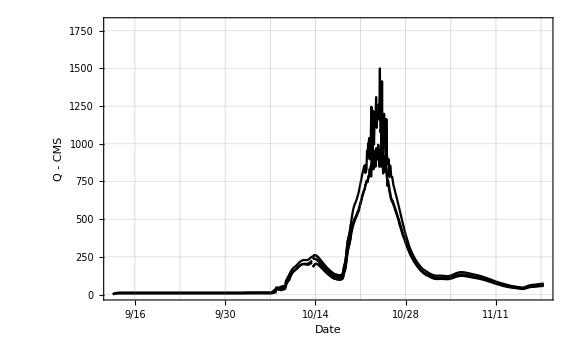

```mathematica
i=9;
klist={9,6,7};
GraphicsGrid[
Partition[
Table[
Show[
Table[
scatterplot[Qgrab[[j,klist[[k]]]],filestarttime,fileendtime,0,1800,"Q - CMS","Date",nodestringnames[[klist[[k]]]],7,True,Black],
{j,3,1,-1}]
]
,{k,1,3}],1]]

Show[
Partition[
Table[
Show[
Table[
scatterplot[Qgrab[[j,klist[[k]]]],filestarttime,fileendtime,0,1800,"Q - CMS","Date",nodestringnames[[klist[[k]]]],7,True,Black],
{j,3,1,-1}]
]
,{k,1,3}],1]]
```

# Tar Banks

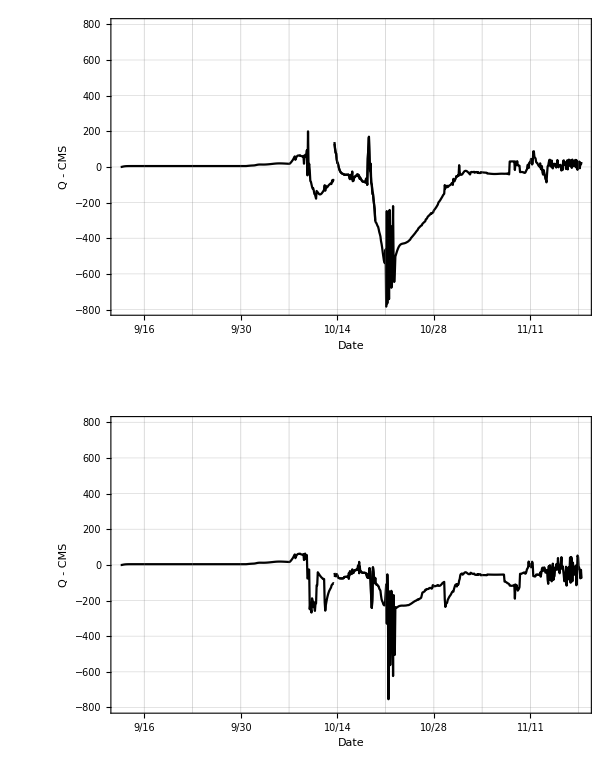

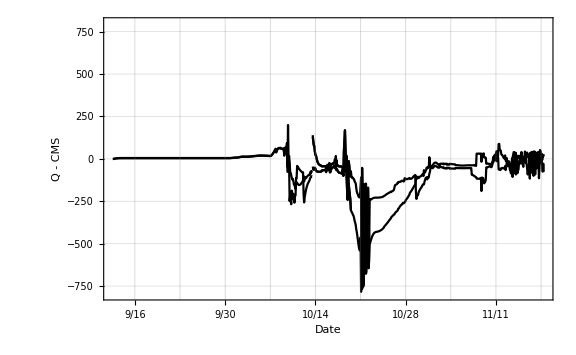

```mathematica
klist={10,11};
GraphicsGrid[
Partition[
Table[
Show[
Table[
scatterplot[Qgrab[[j,klist[[k]]]],filestarttime,fileendtime,-800,800,"Q - CMS","Date",nodestringnames[[klist[[k]]]],7,True,Black],
{j,3,1,-1}]
]
,{k,1,2}],1]]

Show[
Partition[
Table[
Show[
Table[
scatterplot[Qgrab[[j,klist[[k]]]],filestarttime,fileendtime,-800,800,"Q - CMS","Date",nodestringnames[[klist[[k]]]],7,True,Black],
{j,3,1,-1}]
]
,{k,1,2}],1]]
```

# Element Flow downstream (zigfinder)

```mathematica
(*step 1- import spinup file*)
inp={spinupinputfile,hurricaneinputfile,spindowninputfile};

zigQgrab=Table[0,{Length[inp]}];
Do[

inputfile=inp[[storm]];





zigQgrab[[storm]]=Catch[


If[inputfile=="no file",
Throw["error - no file selected"];
];

in=OpenRead[inputfile];
(*STEP 1 - CHECK FOR COMPLETENESS*)
junk=Read[in,String];
stepsheader=Read[in,Number];
junk=Read[in,String];



(*get filelength*)
entries=ReadList[in,String];(*these are all the individual entries*)
filelength=Length[entries];
(*figure out how many output entries there are in the file*)
(*the file has 2 header lines*)

(*at each timestep, there is one line plus one for each segment node*)
perstep=1+Sum[segmentlengths[[i]],{i,1,Length[segmentlengths]}];
nsteps=filelength/perstep;
If[nsteps≠stepsheader,
Throw["error-steps don't match"];
];

(*now that we know the number of lines in each step (perstep) we can import all the data*) 
Close[in];






in=OpenRead[inputfile];

outputlist={"header",Table[0,{nsegs}]};

header=Read[in,String];
junk=Read[in,String];
raw=ReadList[in,Word];
Close[in]
(*clean the entries*)
Do[
If[raw[[i]]=="NaN",
raw[[i]]=-9999,
raw[[i]]=StringReplace[raw[[i]],{"E+"->"*^","E-"->"*^-"}];
raw[[i]]=raw[[i]]//ToExpression]
,{i,1,Length[raw]}];



(*step 1 - partition raw into each timestep entry.*)
(*the quick way to do this is to use nsteps and filelength to get the entries per step.*)
(*note that we can't just use the prior value of "perstep" because at this point, *)
(* "perstep" is in lines, and we need it in numbers*)
(*e.g. each timestep line is one line, 2 numbers, etc*)
perstep=Length[raw]/nsteps;
raw=Partition[raw,perstep];
raw=Transpose[raw];
(*now raw is a bunch of vectorized entries with the following form*)
(*
time
timestep
(for i = 1 -> nsegs)
node i,1
node i,2
node i,3
....
node i,J(i)
segmentnumber(i)
avg_depth(i)
avg_V(i)
segment_Q(i)
*)
(*for the zig segment, we know that there are 11 antecedent segments, followed by 63 elemental fluxes*)
zigindices=2+Sum[segmentlengths[[i]]-1,{i,1,11}]+44+1;
zigQs=raw[[zigindices;;zigindices+62]];
signs=Table[-1^n,{n,1,63}];
zigQscatters=Table[Transpose[{raw[[1]]+filestarttime,Abs[zigQs[[i]]]}],{i,1,63}];
Throw[zigQscatters];
]
,{storm,1,Length[inp]}];
```

```mathematica
Show[
scatterplot[zigQgrab[[2]],filestarttime,fileendtime,"Q - CMS","Date","zig Qs"],
scatterplot[zigQgrab[[1]],filestarttime,fileendtime,"Q - CMS","Date","zig Qs"],
scatterplot[zigQgrab[[3]],filestarttime,fileendtime,"Q - CMS","Date","zig Qs"]
]

Manipulate[
Show[
scatterplot[zigQgrab[[2,i]],filestarttime,fileendtime,"Q - CMS","Date","zig Qs"],
scatterplot[zigQgrab[[1,i]],filestarttime,fileendtime,"Q - CMS","Date","zig Qs"],
scatterplot[zigQgrab[[3,i]],filestarttime,fileendtime,"Q - CMS","Date","zig Qs"]
]
,{i,1,Length[zigQgrab[[2]]],1}]
```

Show::gcomb: Could not combine the graphics objects in Show[« 1 »].

Show[1]
 |  |  |  |

Part::partd: Part specification zigQgrab ⟦ 2, 1 ⟧ is longer than depth of object.

Part::partd: Part specification zigQgrab ⟦ 1, 1 ⟧ is longer than depth of object.

Part::partd: Part specification zigQgrab ⟦ 3, 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[scatterplot[zigQgrab ⟦ 2, 1 ⟧, 3146169600, 3151958400, "Q - CMS", "Date", "zig Qs"], scatterplot[zigQgrab ⟦ 1, 1 ⟧, 3146169600, 3151958400, "Q - CMS", "Date", "zig Qs"], scatterplot[zigQgrab ⟦ 3, 1 ⟧, 3146169600, 3151958400, "Q - CMS", "Date", "zig Qs"]].

Part::partd: Part specification zigQgrab ⟦ 2, 1 ⟧ is longer than depth of object.

Part::partd: Part specification zigQgrab ⟦ 1, 1 ⟧ is longer than depth of object.

Part::partd: Part specification zigQgrab ⟦ 3, 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[scatterplot[zigQgrab ⟦ 2, 1 ⟧, 3146169600, 3151958400, "Q - CMS", "Date", "zig Qs"], scatterplot[zigQgrab ⟦ 1, 1 ⟧, 3146169600, 3151958400, "Q - CMS", "Date", "zig Qs"], scatterplot[zigQgrab ⟦ 3, 1 ⟧, 3146169600, 3151958400, "Q - CMS", "Date", "zig Qs"]].

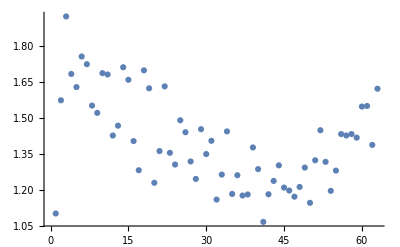

Part::partd: Part specification time ⟦ 1 ⟧ is longer than depth of object.

DateString::arg: Argument time ⟦ 1 ⟧ cannot be interpreted as a date or time input or as a date string format.

Part::partd: Part specification timestepprofile ⟦ 1 ⟧ is longer than depth of object.

Part::pkspec1: The expression False cannot be used as a part specification.

ListPlot::lpn: timestepprofile ⟦ 1 ⟧ is not a list of numbers or pairs of numbers.

Part::partd: Part specification time ⟦ 1 ⟧ is longer than depth of object.

DateString::arg: Argument time ⟦ 1 ⟧ cannot be interpreted as a date or time input or as a date string format.

Part::partd: Part specification timestepprofile ⟦ 1 ⟧ is longer than depth of object.

Part::pkspec1: The expression False cannot be used as a part specification.

ListPlot::lpn: timestepprofile ⟦ 1 ⟧ is not a list of numbers or pairs of numbers.

```mathematica
(*now, just for the spinup, because that's when my Qs are most valid, I want to show the flow at each element face, with element face as my "X" axis and flow as my Y axis, in a "manipulate" box where I can manipulate (animate) time.*)

(* plan: first, strip all time data and store elsewhere.*)
time=Transpose[zigQgrab[[1,1]]][[1]];

ListPlot[Transpose[Transpose[zigQgrab[[1]]][[1]]][[2]]] (*this is the scatter of Qs at the first timestep.*)

timestepprofile=Table[Transpose[Transpose[zigQgrab[[1]]][[i]]][[2]],{i,1,Length[time]}];

Manipulate[
{{DateString[time[[i]]]},
{"Flow at each element, Tar River, starting at handoff pt."},
{"CMS"},
{ListPlot[timestepprofile[[i]]]}
}//MatrixForm,
{i,1,Length[time],1}]
```